### Example 1a |J_11| = q3^2 s_2

```mathematica
DataFile["FinalSingularityA.txt"];
FKin[];SimplifyTrigNotation[];
J11 = FullSimplify[J⟦1;;3⟧];
J11//MatrixForm  (*velocity component*)
FullSimplify[Det[J11]]
```

Joint
1
2
3   Type
revolute
revolute
prismatic   a
0
0
0   α
-Pi/2.
-Pi/2.
0   d
0
0
q3   θ
q1
q2
0

Jacobian  J(6x3)

(q3 s_1 s_2 | -q3 c_1 c_2 | -c_1 s_2
-q3 c_1 s_2 | -q3 c_2 s_1 | -s_1 s_2
0 | q3 s_2 | -c_2)

q3^2 s_2

### Example 1b, |J_11| = q2 c_3

```mathematica
DataFile["FinalSingularityE.txt"];
FKin[];SimplifyTrigNotation[];
J11 = FullSimplify[J⟦1;;3⟧];
J11//MatrixForm  (*velocity component*)
FullSimplify[Det[J11]]
```

Joint
1
2
3   Type
revolute
prismatic
revolute   a
0
0
1   α
-Pi/2.
0
0   d
0
q2
0   θ
q1
0
q3

Jacobian  J(6x3)

(-q2 c_1-c_3 s_1 | -s_1 | -c_1 s_3
c_1 c_3-q2 s_1 | c_1 | -s_1 s_3
0 | 0 | -c_3)

q2 c_3

### Example 1c |J_11|= Cos[q3/2]^2 (2 c_2 c_3-2 (1+c_2) s_3)

```mathematica
DataFile["FinalSingularityF.txt"];
FKin[];SimplifyTrigNotation[];
J11 = FullSimplify[J⟦1;;3⟧];
J11//MatrixForm  (*velocity component*)
FullSimplify[Det[J11]]
```

Joint
1
2
3   Type
revolute
revolute
revolute   a
1
1
1   α
Pi/2.
Pi/2.
0   d
0
1
0   θ
q1
q2
q3

Jacobian  J(6x3)

(-(1+c_2 (1+c_3)) s_1+c_1 (1+s_3) | -2 c_1 Cos[q3/2]^2 s_2 | c_3 s_1-c_1 c_2 s_3
c_1 (1+c_2 (1+c_3))+s_1 (1+s_3) | -2 Cos[q3/2]^2 s_1 s_2 | -c_1 c_3-c_2 s_1 s_3
0 | c_2 (1+c_3) | -s_2 s_3)

Cos[q3/2]^2 (2 c_2 c_3-2 (1+c_2) s_3)

### (2 c_2 c_3-2 (1+c_2) s_3)

```mathematica
Plot3D[ {0,( Cos[x]Cos[y]-(1-Cos[x])Sin[y])},{x,0,2π},{y,0,2π},PlotStyle->{Opacity[0.5],Automatic}]
```

-Graphics3D-

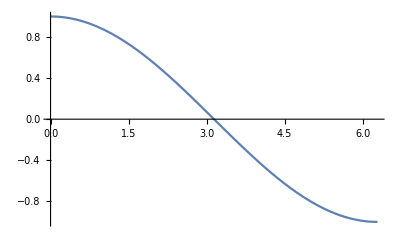

```mathematica
Plot[Cos[q3/2],{q3,0,2π}]
```